#### GRADOS EN INGENIERÍA TELEMÁTICA E INGENIERÍA DE TECNOLOGÍAS DE TELECOMUNICACIÓN Métodos Matemáticos de las Telecomunicaciones (curso 23 - 24) Practica 1. Operadores diferenciales.

Para realizar el producto escalar de dos vectores se utiliza el punto “.” del teclado. Asimismo, para calcular la longitud de un vector se utiliza la orden Norm.

## Ejercicio 1

a) Calcular el producto escalar (3,4)·(-1,2).
b) Calcular el módulo del vector (3,1,-1)

```mathematica
(* A *)
{3,4} . {-1,2}
```

5

```mathematica
(* B *)
```

```mathematica
Norm[{3,1,-1}]
```

√11

## Ejercicio 2

Para realizar el producto vectorial de dos vectores de ℝ^3 Mathematica tiene la orden Cross.

a) Calcular el producto vectorial: (3,-1,2)×(-1,1,2).
b) Sean u, v dos vectores de ℝ^3 demostrar que (|u×v|)^2=(|u|)^2(|v|)^2-(u·v)^2  (se recomienda realizar cada operación paso a paso)

```mathematica
(* A *)

Cross[{3, -1, 2}, { -1, 1, 2}]
```

{-4,-8,2}

```mathematica
(* B *)
u = { u1, u2, u3};
v = { v1, v2, v3};
Cross[u,v]
```

{-u3 v2+u2 v3,u3 v1-u1 v3,-u2 v1+u1 v2}

```mathematica
{-u3 v2+u2 v3,u3 v1-u1 v3,-u2 v1+u1 v2} . {-u3 v2+u2 v3,u3 v1-u1 v3,-u2 v1+u1 v2}
```

(-u2 v1+u1 v2)^2+(u3 v1-u1 v3)^2+(-u3 v2+u2 v3)^2

```mathematica
ladoizquierdo = (-u2 v1+u1 v2)^2+(u3 v1-u1 v3)^2+(-u3 v2+u2 v3)^2;
```

```mathematica
ladodirecho = u.u *  v.v - (u.v)^2;
```

```mathematica
FullSimplify[ladoizquierdo == ladodirecho]
```

True

## Ejercicio 3

Mathematica tiene la orden VectorPlot y VectorPlot3D para dibujar un campo vectorial en  ℝ^2 y  ℝ^3 respectivamente.
Nota. Hay que tener en cuenta que Mathematica no dibuja con precisión la longitud de los vectores.

a) Dibujar con el Mathematica el campo vectorial F(x,y)=(x -y,cos x) en el rectángulo {-2≤x≤2
-2≤y≤2.
b) Dibujar el mismo campo anterior pero con menos vectores.

```mathematica
(* A *)
f[x_, y_] = {x-y, Cos[x]}
```

{x-y,Cos[x]}

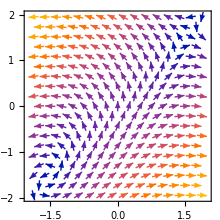

```mathematica
VectorPlot[f[x,y], {x, -2, 2}, { y, -2 , 2}]
```

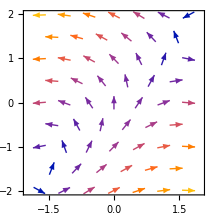

```mathematica
(* B *)
VectorPlot[f[x,y], {x, -2, 2}, { y, -2 , 2}, VectorPoints->7]
```

## Ejercicio 4

a) Dibujar con el Mathematica el campo vectorial F(x,y,z)=(sen(x y),y,z^2) en el cubo Piecewise[{{-1≤x≤1, }, {-1≤y≤1, }, {-1≤z≤1, }}].
b) Dibujar el mismo campo vectorial pero con menos vectores y la cabeza de los vectores en forma de flechas.

```mathematica
(* A *)
VectorPlot3D[{Sin[x*y], y, z^2}, {x,1,-1}, {y,1,-1}, { z, 1, -1}]
```

-Graphics3D-

```mathematica
(* B *)
```

```mathematica
VectorPlot3D[{Sin[x*y], y, z^2}, {x,1,-1}, {y,1,-1}, { z, 1, -1}, VectorPoints->5, VectorStyle->Arrowheads ]
```

-Graphics3D-

## Ejercicio 5

Mathematica tiene la orden Grad para obtener el gradiente de una función ℝ^n→ℝ.
												∇f=((∂f)/(∂x_1),…,(∂f)/(∂x_n))

Calcular el vector gradiente de la función f(x,y,z)=cos(x^2 y)

```mathematica
Grad[Cos[x^2*y], { x,y, z}]
```

{-2 x y Sin[x^2 y],-x^2 Sin[x^2 y],0}

## Ejercicio 6

Mathematica tiene la orden Curl para obtener el rotacional de un campo vectorial F(x,y,z) en ℝ^3.
											∇×F=|i | j | k
∂/(∂x) | ∂/(∂y) | ∂/(∂z)
F_1 | F_2 | F_3|

Calcular el rotacional del campo vectorial F(x,y,z)=(x^2, y^3, x y)

```mathematica
Curl[{x^2, y^3, x*y}, {x,y,z}]
```

{x,-y,0}

## Ejercicio 7

Mathematica tiene la orden Div para obtener la divergencia de un campo (∇·F).
											∇·F=((∂F_1)/(∂x_1)+...+(∂F_n)/(∂x_n))

Calcular la divergencia del campo vectorial F(x,y)=(Cos(x y),sen y)

```mathematica
Div[{Cos[x*y], Sin[y]}, {x,y}]
```

Cos[y]-y Sin[x y]

## Ejercicio 8

Mathematica tiene la orden Laplacian para calcular el lapaciano que se puede aplicar tanto a una función como a un campo vectorial. 
										Δ f=∇^2 f=∇·(∇f)=(∂^2 f)/(∂x_1^2)+...+(∂^2 f)/(∂x_n^2)
										Δ F=∇^2 F=(∇^2 F_1,...,∇^2 F_n)

a) Calcular Δ f=∇^2 f siendo f(x,y)=x sen y
a) Calcular Δ F=∇^2 F siendo F(x,y)=(x^3,x y^2)

```mathematica
(* A *)
```

```mathematica
Laplacian[{x*Sin[y]}, {x,y}]
```

{-x Sin[y]}

```mathematica
(* B *)
```

```mathematica
Laplacian[{x^3, x * y ^2}, {x,y}]
```

{6 x,2 x}

## Ejercicio 9

Sean los siguientes campos vectoriales:
F(x,y,z)=(ⅇ^(x+z),y^2,x z)
G(x,y,z)=(x y,x+z,0)
f(x,y,z)=x-y^2+z^3
Comprobar las siguientes identidades del análisis vectorial (desarrollando cada elemento que aparezca en la igualdad):
a) div(f F)=f div F+F·∇f o lo que es lo mismo ∇(f F)=f ∇·F+F·∇f
b) rot(F+G)=rot F+rot G o lo que es lo mismo ∇×(F+G)=∇×F+∇×G

```mathematica
F[x_,y_,z_] = {E^(x+z), y ^2, x * z};
G[x_,y_,z_] = {x*y, x + z, 0 };
f[x_,y_,z_] = {x - y ^2 + z^3};
```

```mathematica
f[x,y,z] * F[x,y,z]
```

{ⅇ^(x+z) Sin[x y],y^3,xz z^2}

```mathematica
ladoizquierdo = Div[{ⅇ^(x+z) * Sin[x* y],y^3,x* z^3} , {x,y,z}] 
ladodirecho = f[x,y,z] * Div[F[x,y,z], {x,y,z}] + F[x,y,z] . Grad[f[x,y,z], {x,y,z}];
```

3 y^2+3 x z^2+ⅇ^(x+z) y Cos[x y]+ⅇ^(x+z) Sin[x y]

```mathematica
FullSimplify[ladoizquierdo == ladodirecho]
```

3 (y^2+x z^2)+ⅇ^(x+z) (y Cos[x y]+Sin[x y])=={ⅇ^(x+z) y Cos[x y]+(ⅇ^(x+z)+x+2 y) Sin[x y],y (x+3 y)+ⅇ^(x+z) (y+x Cos[x y]),(ⅇ^(x+z)+3 x+2 y) z^2}

```mathematica
(* B *)
ladoizquierdo = Curl[F[x,y,z] + G[x,y,z], {x,y,z}];
```

```mathematica
ladodirecho = Curl[F[x,y,z], {x,y,z}] + Curl[G[x,y,z], {x,y,z}];
```

```mathematica
FullSimplify[ladoizquierdo == ladodirecho]
```

True